```mathematica
k = 12;
h = 0.16;

df[x_] := -k*x
f[0.0] = 1;
f[t_] := f[t-h] + df[f[t-h]]*h

g[0.0] = 1;
g[t_] := g[t-h] / (1 + h*k)

Slider[Dynamic[k], {0, 50}]
Slider[Dynamic[h], {0.05, 1}]

Dynamic[Show[Plot[E^(-k*t), {t, 0, 1}, PlotRange->{-1, 1}], DiscretePlot[{f[t], g[t]}, {t, 0, 1, h}, Joined->True, PlotRange->{-1, 1}]]]
```

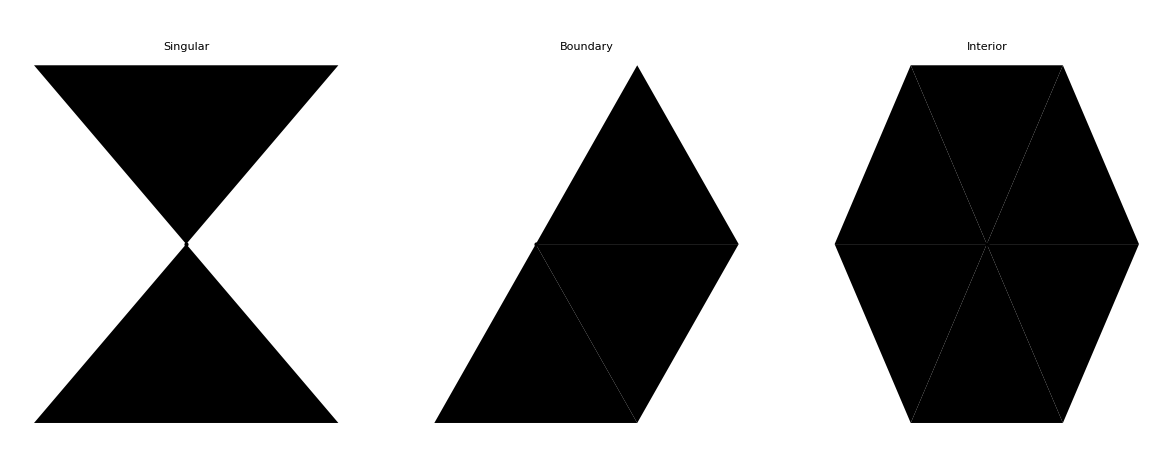

/Users/miles/Kiln/projects/fem/Figures.pdf

```mathematica
apex = {1/2, Sqrt[3]/2};
tri = {{0,0}, {1,0}, apex};
style = {FaceForm[None],EdgeForm[Blue],AbsolutePointSize[8]};

fig = GraphicsRow[{
Graphics[{Polygon[tri], Rotate[Polygon[tri], 180Degree, apex],Point[apex]},PlotLabel->"Singular", BaseStyle->style],

Graphics[{
Rotate[Polygon[tri],0Degree],
Rotate[Polygon[tri],60Degree, apex],
Rotate[Polygon[tri],120Degree, apex], Point[apex]},PlotLabel->"Boundary",BaseStyle->style],

Graphics[{
Rotate[Polygon[tri],0Degree],
Rotate[Polygon[tri],60Degree, apex],
Rotate[Polygon[tri],120Degree, apex],
Rotate[Polygon[tri],180Degree, apex],
Rotate[Polygon[tri],240Degree, apex],
Rotate[Polygon[tri],300Degree, apex] ,Point[apex]},PlotLabel->"Interior", BaseStyle->style]}]

Export[FileNameJoin[{NotebookDirectory[], "figures.pdf"}],fig]
```

{{0.72,0.08},{1.2,0.08},{1.2,0.16}}

{{0.72,0.16},{0.72,0.08},{1.2,0.16}}

{{0.48,0.08},{0.4,0.08},{0.96,0.12}}

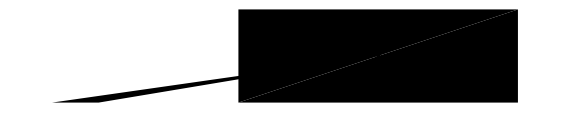

```mathematica
tri1 = {{0.720000,0.080000},{1.200000,0.080000},{1.200000,0.160000}}
tri2 = {{0.720000,0.160000},{0.720000,0.080000},{1.200000,0.160000}}
tri3 = {{0.480000,0.080000}, {0.400000,0.080000}, {0.960000,0.120000}}
Graphics[{Polygon[tri1], Polygon[tri3], Polygon[tri2], Point[{0.96, 0.12}, Style->Red]}]
```

{{{-0.351517,0.960726},{-20.,-20.},{-0.090693,0.649801}},{{-20.,-20.},{20.,-20.},{0.053043,0.581536}},{{-0.090693,0.649801},{-20.,-20.},{0.053043,0.581536}},{{0.053043,0.581536},{20.,-20.},{0.316703,1.07827}}}

{0.,0.}

{{{-0.351517,0.960726},{-20.,-20.}},{{-0.090693,0.649801},{-0.351517,0.960726}},{{-20.,-20.},{20.,-20.}},{{0.053043,0.581536},{-0.090693,0.649801}},{{20.,-20.},{0.316703,1.07827}},{{0.316703,1.07827},{0.053043,0.581536}}}

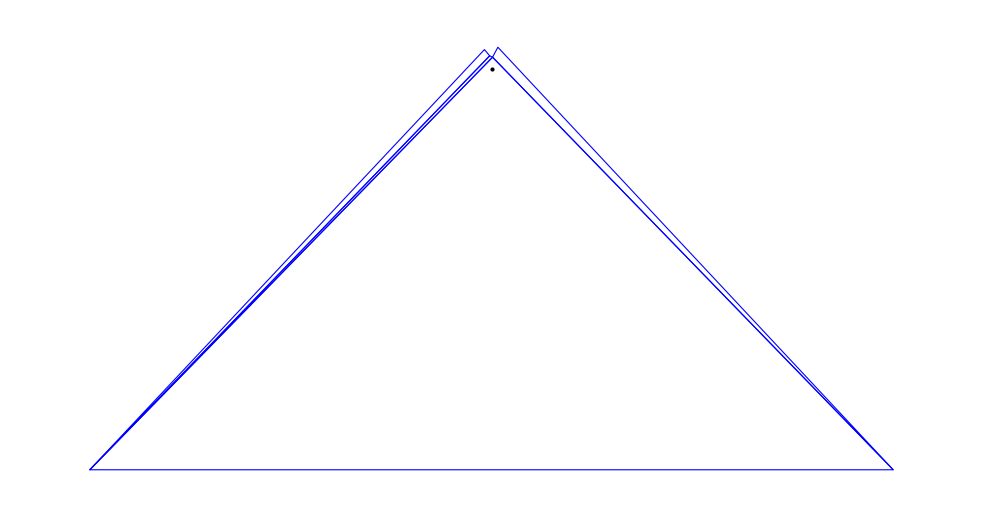

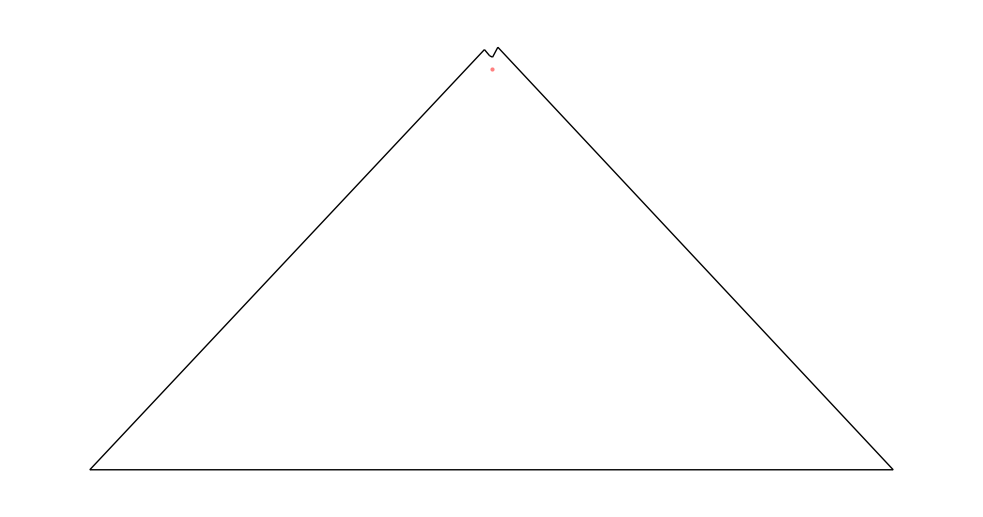

```mathematica
tris={{{-0.351517,0.960726},{-20.000000,-20.000000},{-0.090693,0.649801}},{{-20.000000,-20.000000},{20.000000,-20.000000},{0.053043,0.581536}},{{-0.090693,0.649801},{-20.000000,-20.000000},{0.053043,0.581536}},{{0.053043,0.581536},{20.000000,-20.000000},{0.316703,1.078273}}}
pr={0.000000,0.000000}
edges={{{-0.351517,0.960726},{-20.000000,-20.000000}},{{-0.090693,0.649801},{-0.351517,0.960726}},{{-20.000000,-20.000000},{20.000000,-20.000000}},{{0.053043,0.581536},{-0.090693,0.649801}},{{20.000000,-20.000000},{0.316703,1.078273}},{{0.316703,1.078273},{0.053043,0.581536}}}



Graphics[{FaceForm[None],EdgeForm[Blue],Polygon/@tris, Point[pr]}]
Graphics[{FaceForm[None],EdgeForm[Blue], Line/@edges, Pink, Point[pr]}]
```